```mathematica
fraw[x_]:=(x^2-25)^2/4
```

```mathematica
f[x_]:=fraw[16 x]
```

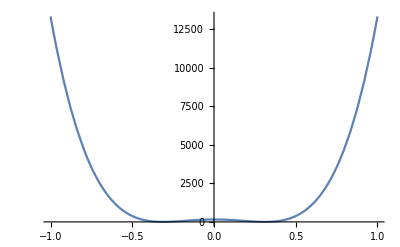

```mathematica
Plot[f[x],{x,-1,1}]
```

```mathematica
ClearAll[g];
```

```mathematica
g[θ_]:=f[Cos[θ]]
```

```mathematica
θ[k_]:=(k-1/2) π/(n+1);
```

```mathematica
n=10;
```

```mathematica
c=2/(n+1) N[Table[Sum[g[θ[k]] Cos[i θ[k]],{k,1,n+1}],{i,0,n}]];
```

```mathematica
c
```

{9400.5,0.,6592.,0.,2048.,0.,-1.65363×10^-12,0.,0.,0.,3.30725×10^-13}

```mathematica
Length[c]
```

11

```mathematica
ClearAll[chebapprox];chebapprox[x_,n_]:=Sum[If[i==0||i==n,1/2,1] c[[i+1]] ChebyshevT[i,x],{i,0,n}]
```

```mathematica
error[n_]:=Block[{c},
c=2/(n+1) N[Table[Sum[g[(k-1/2) π/(n+1)] Cos[i (k-1/2) π/(n+1)],{k,1,n+1}],{i,0,n}]];
ca[x_]:=Sum[If[i==0||i==n,1/2,1] c[[i+1]] ChebyshevT[i,x],{i,0,n}];
N[Sqrt[Integrate[(ca[x]-f[x])^2,{x,-1,1}]]]
]
```

```mathematica
Table[error[n],{n,2,20}]
```

{3891.29,2031.68,1015.84,1.64102×10^-12,1.10947×10^-12,1.15043×10^-12,1.05621×10^-12,1.02508×10^-12,2.02734×10^-12,1.52127×10^-12,1.43727×10^-12,1.86605×10^-12,1.19145×10^-12,1.3952×10^-12,1.99291×10^-12,2.70691×10^-12,8.61108×10^-13,1.33039×10^-12,2.21293×10^-12}

2.65589×10^-12

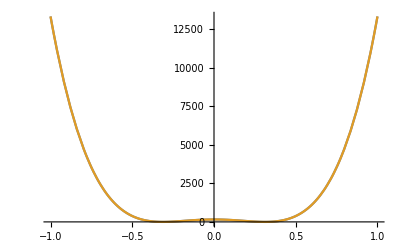

```mathematica
n=20;
c=2/(n+1) N[Table[Sum[g[θ[k]] Cos[i θ[k]],{k,1,n+1}],{i,0,n}]];
Print[N[Sqrt[Integrate[(chebapprox[x,11]-f[x])^2,{x,-1,1}]]]];Plot[{f[x],chebapprox[x,n]},{x,-1,1}]
```